## Some 2D orthogonal coordinate systems

PHYS/MATH 4325
Texas Tech University
Prof. Katharine Long

The most important 2D orthogonal coordinate systems are Cartesian and plane polar; you need to learn to work comfortably with both. Several others allow separation of variables of the wave and Schrodinger equations (if you don’t know what “separation of variables” means, fear not, by the end of the semester you will). Don’t worry: we won’t do separation of variables in any of the oddball systems like bipolar coordinates; that’s horribly messy and the applications are specialized. We will (later this semester) study separation of variables for partial differential equations in Cartesian, plane polar, and (in 3D) cylindrical and spherical coordinates; there are many important applications in these systems, from atoms to galaxies and many things in between. 

Techniques based on functions of complex variables can construct very general orthogonal coordinate systems in 2D, in which the Laplace equation of electrostatics, magnetostatics, and ideal fluid flow is easily solvable. We will study complex variables in 4326, though we’ll only briefly touch on that application of them (the technique is known as conformal mapping; it is, unfortunately, only applicable in 2D).

```mathematica
plotCoords[R_,{u_,uMin_,uMax_,nu_:20},{v_,vMin_,vMax_,nv_:20},args___]:=
Show[
ParametricPlot[Table[R[u,v],{u,uMin,uMax,(uMax-uMin)/nu}],
{v,vMin,vMax},PlotStyle->RGBColor[0,0.25,0.75],args],ParametricPlot[Table[R[u,v],{v,vMin,vMax,(vMax-vMin)/nv}],
{u,uMin,uMax},PlotStyle->Red,args]
]
```

#### Cartesian coordinates (2D)

Too many applications to list

```mathematica
Subscript[r, cart2D][x_,y_]={x,y}
```

{x,y}

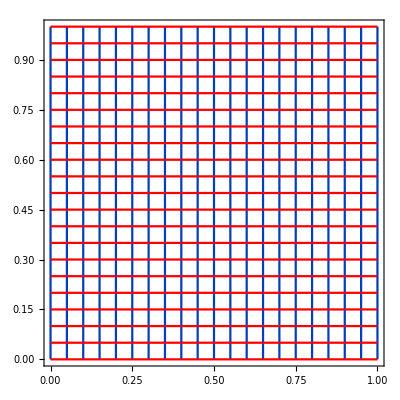

```mathematica
plotCoords[Subscript[r, cart2D],{x,0,1},{y,0,1}]
```

#### Plane polar coordinates

Too many applications to list

```mathematica
Subscript[r, pol][ρ_,ϕ_]={ρ Cos[ϕ],ρ Sin[ϕ]}
```

{ρ cos(ϕ),ρ sin(ϕ)}

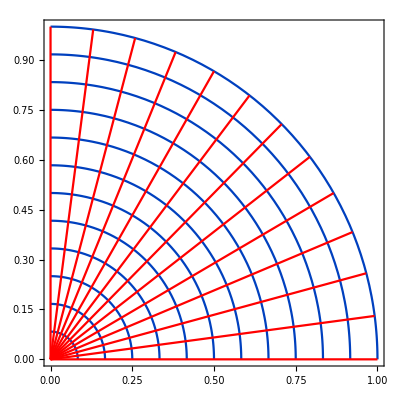

```mathematica
plotCoords[Subscript[r, pol],{ρ,0,1,12},{ϕ,0,Pi/2,12}]
```

#### Elliptical coordinates

See Hassani, prob 2.32

Some applications:

Waveguide with elliptical cross-section

Ideal flow out of a slit

Electrostatic potential from an infinitely long strip with finite width

```mathematica
Subscript[r, ell][u_,v_]={Cosh[u]Cos[v],Sinh[u]Sin[v]}
```

{cosh(u) cos(v),sinh(u) sin(v)}

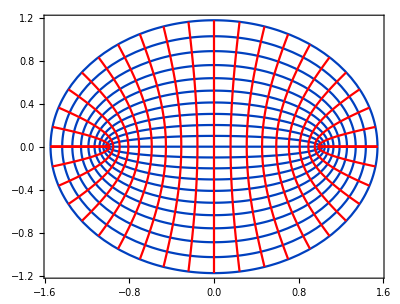

```mathematica
plotCoords[Subscript[r, ell],{u,-1,1},{v,0,Pi}]
```

#### Plane parabolic coordinates

See Hassani, prob 2.33

Some applications:

Waveguide with parabolic cross-section

Parabolic reflector

```mathematica
Subscript[r, par][u_,v_]={u^2-v^2, 2 u v}
```

{u^2-v^2,2 u v}

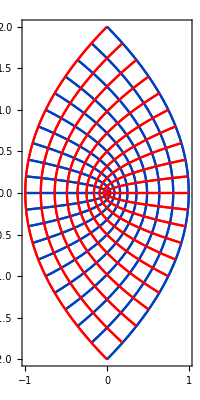

```mathematica
plotCoords[Subscript[r, par],{u,-1,1},{v,-1,1}]
```

#### Bipolar coordinates (2D)

See Hassani, problem 2.34

Some applications

Electrostatic potential due to two cylinders

Magnetostatic potential due to two wires

Ideal flow around two cylinders

```mathematica
Subscript[r, bp][u_,v_]={Sinh[u],Sin[v]}/(Cosh[u]+Cos[v])
```

{(sinh(u))/(cosh(u)+cos(v)),(sin(v))/(cosh(u)+cos(v))}

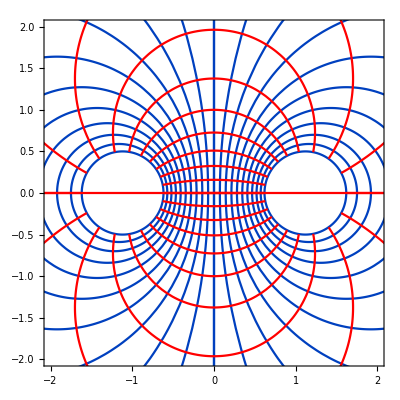

```mathematica
plotCoords[Subscript[r, bp],{u,-ArcSinh[2],ArcSinh[2]},{v,0,2Pi},PlotRange->{{-2,2},{-2,2}}]
```